# Estudo sobre espalhamento de campos acústicos.

Ultima Versão : 23/05/2019

Descrição: Aqui, vamos resolver as equações de contorno para a propagação e espalhamento acústico em coordenadas esféricas.

## Inicialização

## Coeficientes de feixe

```mathematica
Gpw[l_,f_,z0_] =2*Sqrt[π]*Sqrt[2l+1] *ⅈ^l * Exp[(-ⅈ 2π f z0/cE)] ;
Gest[l_,f_,z0_] =2*Sqrt[(4π)(2l+1)]  Re[ⅈ^l Exp[(-ⅈ 2π f z0/cE)]] ; (*O coefficiente original estava errado, alterei para o correto*)
Gbes[l_,m_,β_,z0_,o_]=ⅈ^(l-m)Sqrt[(2l+1) 4π]Sqrt[((l-m)!)/((l+m)!)]LegendreP[l,m,Cos[β]]Exp[-ⅈ 2π f/cE Cos[β] z0]KroneckerDelta[o,m];
```

## Variáveis dos meios

```mathematica
ρE= 997; (*agua*)
ρI= 1275/1000;(*ar*)
cE=1482;(*agua*)
cI=34087/100;(*ar*)
α =(ρI cI)/(ρE cE);
z=0;
NMax=15;
β=π/4;
```

## Onda Plana

### Espalhamento

```mathematica
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_,f_,a_,z0_]:= Gpw[l,f,z0]( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));(*Multipolo do Campo Espalhado*)
Alm[l_,f_,a_,z0_]:= Gpw[l,f,z0]( ( DH[l,2π f /cE a]SphericalBesselJ[l,2π f /cE a]-SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cE a])/(SphericalBesselJ[l,2π f /cI a] DH[l,2π f /cE a]- SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cI a]/α))  ;(*Multipolo do Campo Interno*)
Pesp[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalHankelH1[l,2π f /cE r] SphericalHarmonicY[l,0,θ,ϕ] Clm[l,f,a,z0],{l,0,NMax}];
Pinc[r_,θ_,ϕ_,f_,z0_]:=Sum[SphericalBesselJ[l,2π f /cE r]SphericalHarmonicY[l,0,θ,ϕ] Gpw[l,f,z0],{l,0,NMax}]; 
PincExato[x_,y_,f_]=Exp[-ⅈ 2π f /cE x];
Pint[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalBesselJ[l,2π f /cI r]SphericalHarmonicY[l,0,θ,ϕ] Alm[l,f,a,z0],{l,0,NMax}]; 
PTot[r_,θ_,ϕ_,f_,a_,z0_]:=Piecewise[{{Pint[r,θ,ϕ,f,a,z0],r<a},{Pesp[r,θ,ϕ,f,a,z0]+Pinc[r,θ,ϕ,f,z0],r≥a}}];
```

Colocar aqui só a parte do codigo para gerar a figuras de espalhamento nos 3 regimes

```mathematica
Parâmetro do grid
```

```mathematica
a1=25 10^(-7);
a2=25 10^(-6);
a3=48 10^(-5);
pontos=15;
f=10000000;
samplePoints=8000;
NMax=55;
```

```mathematica
Fatores ka
```

```mathematica
2π f /cE a1//N
2π f /cE a2//N
2π f /cE a3//N

ka1=2π f /cE a1;
ka2=2π f /cE a2;
ka3=2π f /cE a3;
```

0.105992

1.05992

20.3504

```mathematica
GridXY1=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-3 ka1,8ka1,ka1/pontos},{y,-3 ka1,3 ka1,ka1/pontos}],1],{0,0}],samplePoints];
GridXY2=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-3 ka2,8ka2,ka2/pontos},{y,-3 ka2,3 ka2,ka2/pontos}],1],{0,0}],samplePoints];
GridXY3=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-3 ka3,8ka3,ka3/pontos},{y,-3 ka3,3 ka3,ka3/pontos}],1],{0,0}],samplePoints];
```

```mathematica
DadosTot1=ParallelMap[{(#[[1]])/ka1,(#[[2]])/ka1,N[Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a1,z]],50]}&,GridXY1];
```

```mathematica
DadosTot2=ParallelMap[{(#[[1]])/ka2,(#[[2]])/ka2,N[Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a2,z]],50]}&,GridXY2];
```

```mathematica
DadosTot3=ParallelMap[{(#[[1]])/ka3,(#[[2]])/ka3,N[Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a3,z]],50]}&,GridXY3];
```

```mathematica
LogDadosTot1={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot1;
LogDadosTot2={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot2;
LogDadosTot3={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot3;
```

```mathematica
Max1=Max[DadosTot1[[All,3]],DadosTot2[[All,3]],DadosTot3[[All,3]]];
MaxLog1=Max[Log[DadosTot1[[All,3]]+0.00001],Log[DadosTot2[[All,3]]+0.00001],Log[DadosTot3[[All,3]]+0.00001]];
```

```mathematica
Não-normalizado
```

```mathematica
figTot1=Show[ListDensityPlot[DadosTot1,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka1,0.1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]]
```

```mathematica
figTot2=Show[ListDensityPlot[DadosTot2,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka2,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]]
```

```mathematica
figTot3=Show[ListDensityPlot[DadosTot3,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka3,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
```

```mathematica
figLogTot1=Show[ListDensityPlot[LogDadosTot1,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka1,0.1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
```

```mathematica
figLogTot2=Show[ListDensityPlot[LogDadosTot2,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka2,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
```

```mathematica
figLogTot3=Show[ListDensityPlot[LogDadosTot3,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka3,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
```

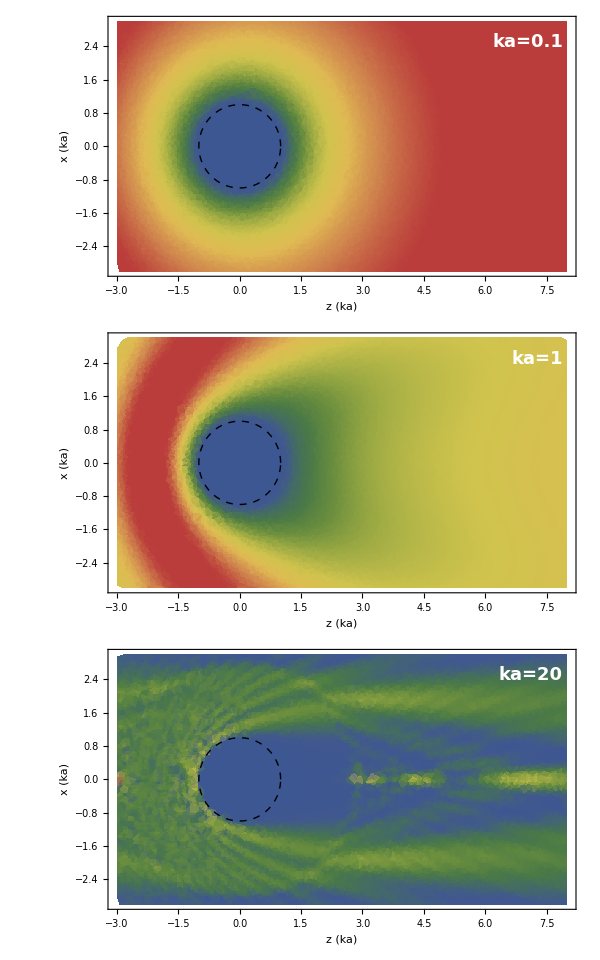

```mathematica
GraphicsGrid[{{figTot1},{figTot2},{figTot3}},ImageSize->600,Frame->None,Spacings->{-30, -10}]
```

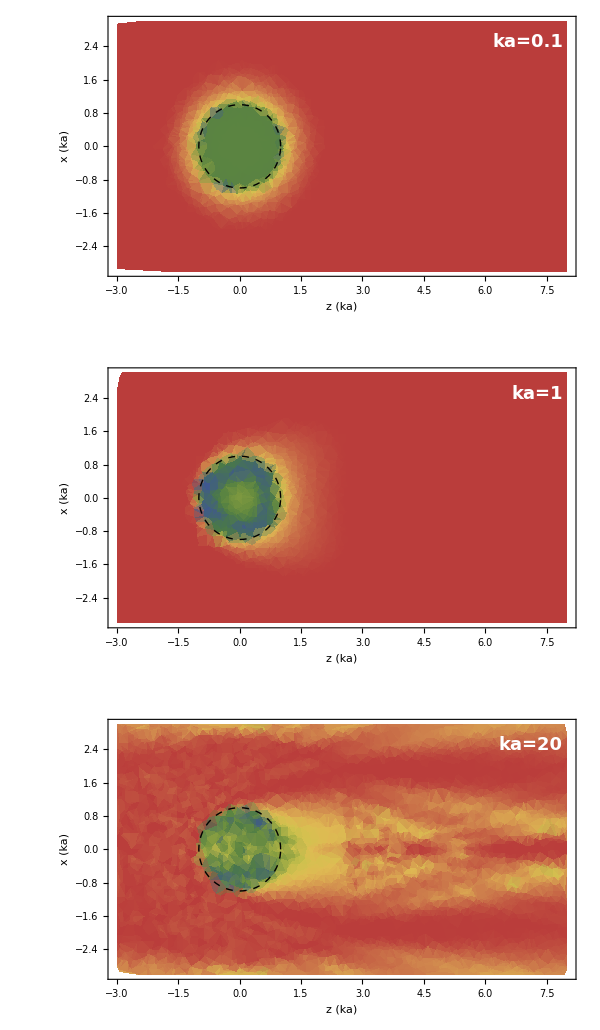

```mathematica
comparacoes=Legended[GraphicsGrid[{{figLogTot1},{figLogTot2},{figLogTot3}},ImageSize->600],Placed[BarLegend[{"DarkRainbow",{-1,1}},LegendMarkerSize->800,LegendLayout->"Row",Ticks->None],Below]]
```

```mathematica
Gerar a força em funcao do tamanho
```

```mathematica
PressaoRadiacaoZPlana[z0_,f_,a_,Nmax_Integer?Positive]:=Module[{Cp,Gp},
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_]= ( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Cp=Table[(2Clm[l] Conjugate[Clm[l+1]]+Clm[l]+Conjugate[Clm[l+1]]),{l,0,Nmax+2}];
Gp=Table[Gpw[l,f,z0] Conjugate[Gpw[l+1,f,z0]],{l,0,Nmax+2}];
N[Im[Sum[Sqrt[(l+1 )( l+1)/((2l+1)(2l+3))]Cp[[l+1]]Gp[[l+1]],{l,0,Nmax}]/(2π f /cE a)^2 ]]]
```

```mathematica
k=2π f /cE;
```

```mathematica
f
```

10000000

```mathematica
Clear[a]
```

```mathematica
Clm[l_,a_]= ( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
```

```mathematica
temp=ParallelTable[{ka,N[Abs[Sum[Clm[l,ka/k],{l,0,Round[ka]}]]]},{ka,1,200,3}]
```

{{1,1.00265},{4,2.53793},{7,4.01263},{10,5.48221},{13,6.90953},{16,8.41723},{19,9.92254},{22,11.4299},{25,12.9577},{28,14.5022},{31,16.0473},{34,17.6483},{37,19.2336},{40,20.865},{43,22.3758},{46,23.9711},{49,25.5406},{52,27.1103},{55,28.626},{58,30.1175},{61,31.6186},{64,33.0548},{67,34.5416},{70,36.0788},{73,37.4024},{76,38.8731},{79,40.3151},{82,41.8865},{85,43.2616},{88,44.7339},{91,46.276},{94,47.4788},{97,49.3317},{100,50.8873},{103,52.4537},{106,54.0791},{109,55.6019},{112,57.0086},{115,58.7736},{118,60.3113},{121,61.7607},{124,63.3265},{127,64.8261},{130,66.2584},{133,67.7304},{136,69.1523},{139,70.6557},{142,72.0525},{145,73.4997},{148,74.9639},{151,76.3835},{154,77.9318},{157,79.4482},{160,80.8885},{163,82.6493},{166,83.9956},{169,85.5341},{172,87.2085},{175,88.7549},{178,90.3961},{181,91.8881},{184,93.4296},{187,94.945},{190,96.5051},{193,98.4501},{196,99.4927},{199,100.879}}

```mathematica
temp
```

{{1,1.00265},{4,2.53793},{7,4.01263},{10,5.48221},{13,6.90953},{16,8.41723},{19,9.92254},{22,11.4299},{25,12.9577},{28,14.5022},{31,16.0473},{34,17.6483},{37,19.2336},{40,20.865},{43,22.3758},{46,23.9711},{49,25.5406},{52,27.1103},{55,28.626},{58,30.1175},{61,31.6186},{64,33.0548},{67,34.5416},{70,36.0788},{73,37.4024},{76,38.8731},{79,40.3151},{82,41.8865},{85,43.2616},{88,44.7339},{91,46.276},{94,47.4788},{97,49.3317},{100,50.8873},{103,52.4537},{106,54.0791},{109,55.6019},{112,57.0086},{115,58.7736},{118,60.3113},{121,61.7607},{124,63.3265},{127,64.8261},{130,66.2584},{133,67.7304},{136,69.1523},{139,70.6557},{142,72.0525},{145,73.4997},{148,74.9639},{151,76.3835},{154,77.9318},{157,79.4482},{160,80.8885},{163,82.6493},{166,83.9956},{169,85.5341},{172,87.2085},{175,88.7549},{178,90.3961},{181,91.8881},{184,93.4296},{187,94.945},{190,96.5051},{193,98.4501},{196,99.4927},{199,100.879}}

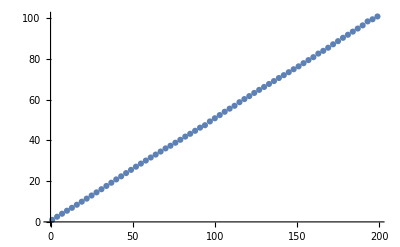

```mathematica
ListPlot[temp]
```

```mathematica
Gpw[l,ff,0]Conjugate[Gpw[l+1,ff,0]]
```

4 ⅈ^l √(1+2 l) π Conjugate[ⅈ^(1+l) √(1+2 (1+l))]

```mathematica
ForceZPlana[0,f,60/k,65]
```

11239.2

```mathematica
R
```

R

```mathematica
FzDataR
```

{{1,1.48471},{4,43.5349},{7,142.201},{10,297.863},{13,510.395},{16,779.729},{19,1105.79},{22,1488.58},{25,1927.91},{28,2424.17},{31,2976.96},{34,3586.36},{37,4252.4},{40,4975.04},{43,5754.31},{46,6590.22},{49,7482.65},{52,8431.73},{55,9437.37},{58,10499.6},{61,11618.5},{64,12793.9},{67,14025.8},{70,15314.4},{73,16659.7},{76,18061.4},{79,19519.7},{82,21034.6},{85,22606.1},{88,24234.1},{91,25918.7},{94,27659.1},{97,29457.6},{100,31311.9},{103,33217.1},{106,35190.2},{109,37214.2},{112,39294.8},{115,41431.9},{118,43625.5},{121,45875.8},{124,48182.6},{127,50546.},{130,52965.9},{133,55442.5},{136,57975.4},{139,60565.1},{142,63211.3},{145,65913.6},{148,68673.3},{151,71489.1},{154,74361.5},{157,77288.2},{160,80276.},{163,83316.9},{166,86416.7},{169,89571.8},{172,Indeterminate},{175,Indeterminate},{178,Indeterminate},{181,Indeterminate},{184,Indeterminate},{187,Indeterminate},{190,Indeterminate},{193,Indeterminate},{196,Indeterminate},{199,Indeterminate}}

```mathematica
FzDataR=ParallelTable[{ka,PressaoRadiacaoZPlana[0,f,ka/k,Round[ka+5]]},{ka,1/10,100,2/10}];
```

$Aborted

```mathematica
FzDataR1=ParallelTable[{ka,PressaoRadiacaoZPlana[0,f,ka/k,Round[ka+5]]},{ka,1/100,1.05,1/20}];
```

```mathematica
FzDataR2=ParallelTable[{ka,PressaoRadiacaoZPlana[0,f,ka/k,Round[ka+5]]},{ka,1,2,1/20}];
```

```mathematica
FzDataR3=ParallelTable[{ka,PressaoRadiacaoZPlana[0,f,ka/k,Round[ka+5]]},{ka,2,6,1/2000}];
```

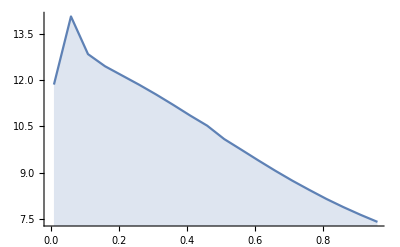

```mathematica
ListLinePlot[FzDataR1,Filling->Axis]
```

```mathematica
Show[ListLinePlot[FzDataR1,Filling->Axis],ListLinePlot[FzDataR3,Filling->Axis]]
```

-Graphics-

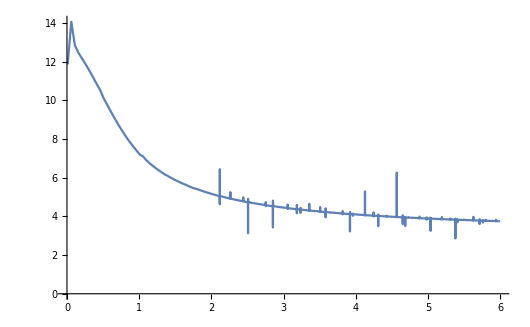

```mathematica
graf=ListLinePlot[Union[FzDataR1,FzDataR3,FzDataR2],PlotRange->All]
```

```mathematica
dados=Union[{FzDataR1,FzDataR3,FzDataR2}]
```

{{{1/100,11.8536},{3/50,14.0546},{11/100,12.8374},{4/25,12.4454},{21/100,12.1474},{13/50,11.8495},{31/100,11.5336},{9/25,11.1994},{41/100,10.8534},{23/50,10.5252},{51/100,10.0923},{14/25,9.7505},{61/100,9.40449},{33/50,9.06894},{71/100,8.74846},{19/25,8.44864},{81/100,8.15871},{43/50,7.89366},{91/100,7.64685},{24/25,7.41637},{101/100,7.18534}},{1},{{2,5.16457},{4001/2000,5.16405},{2001/1000,5.16352},{4003/2000,5.163},{1001/500,5.16247},7991,{2999/500,3.74892},{11997/2000,3.74886},{5999/1000,3.7488},{11999/2000,3.74873},{6,3.74867}}}
 |  |  |  |

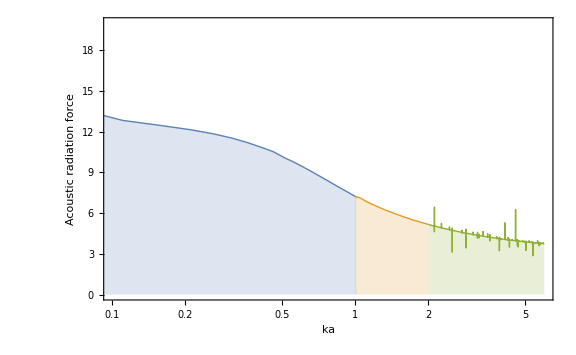

```mathematica
ListLogLinearPlot[dados,PlotRange->{{1/10,6},{0,20}},PlotTheme->"Detailed",LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm["ka"],24,Black],Style[HoldForm["Acoustic radiation force"],24,Black]},PlotRange->All,FrameTicksStyle->Directive[Black,18],Joined->True,ImageSize->Large,PlotStyle->{{Thick}},Filling->Bottom]
```

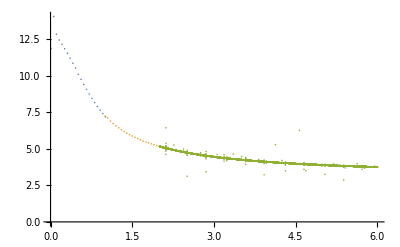

```mathematica
ListPlot[dados,PlotRange->All]
```

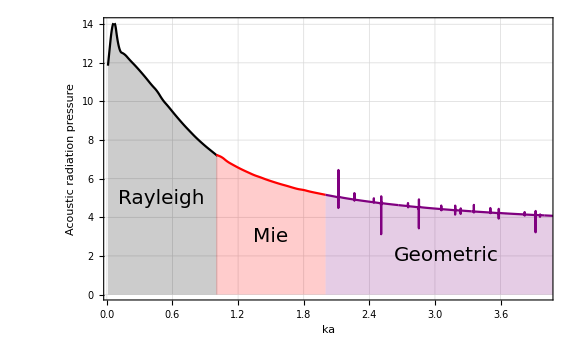

```mathematica
forcaka=Show[ListLinePlot[dados,PlotRange->{{0.05,4},All},PlotStyle->{Black,Red,Purple},PlotTheme->"Detailed",LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm["ka"],24,Black],Style[HoldForm["Acoustic radiation pressure"],24,Black]},PlotRange->All,FrameTicksStyle->Directive[Black,18],Joined->True,ImageSize->Large,PlotStyle->{{Thick}},Filling->Axis,InterpolationOrder->2],Graphics[Text[Style["Rayleigh",20],{.5,5}]],Graphics[Text[Style["Mie",20],{1.5,3}]],Graphics[Text[Style["Geometric",20],{3.1,2}]]]
```

```mathematica
Export["forcaka.png",forcaka,ImageResolution->500]
```

forcaka.png

## Onda Estacionaria

Colocar aqui um plot da intensidade da onda estacionaria ao longo de Z, junto com a Fz, para os 3 tamanhos de espalhador.

```mathematica
Clm[l_,f_,a_,z0_]:= Gest[l,f,z0]( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Alm[l_,f_,a_,z0_]:= Gest[l,f,z0]( ( DH[l,2π f /cE a]SphericalBesselJ[l,2π f /cE a]-SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cE a])/(SphericalBesselJ[l,2π f /cI a] DH[l,2π f /cE a]- SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cI a]/α))  ;
Pesp[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalHankelH1[l,2π f /cE r] SphericalHarmonicY[l,0,θ,ϕ] Clm[l,f,a,z0],{l,0,NMax}];
Pinc[r_,θ_,ϕ_,f_,z0_]:=Sum[SphericalBesselJ[l,2π f /cE r]SphericalHarmonicY[l,0,θ,ϕ] Gest[l,f,z0],{l,0,NMax}]; 
Pint[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalBesselJ[l,2π f /cI r]SphericalHarmonicY[l,0,θ,ϕ] Alm[l,f,a,z0],{l,0,NMax}]; 
PTot[r_,θ_,ϕ_,f_,a_,z0_]:=Piecewise[{{Pint[r,θ,ϕ,f,a,z0],r<a},{Pesp[r,θ,ϕ,f,a,z0]+Pinc[r,θ,ϕ,f,z0],r≥a}}];
```

```mathematica
Parâmetro do grid
```

```mathematica
a1=59 10^(-5);
a2=59 10^(-4);
a3=59 10^(-3);
pontos=20;
samplePoints=500;
f=40000;
k=(2 f π)/cE;
NMax=25;
```

```mathematica
2π f /cE a1//N
2π f /cE a2//N
2π f /cE a3//N

ka1=2π f /cE a1;
ka2=2π f /cE a2;
ka3=2π f /cE a3;
```

0.100056

1.00056

10.0056

```mathematica
Definição das forças
```

```mathematica
ForceZEstacionaria[z0_,f_,a_,Nmax_Integer?Positive]:=Module[{Cp,Gp},
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_]= ( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Cp=Table[(2Clm[l] Conjugate[Clm[l+1]]+Clm[l]+Conjugate[Clm[l+1]]),{l,0,NMax}];
Gp=Table[Gest[l,f,z0] Conjugate[Gest[l+1,f,z0]],{l,0,NMax}];
N[Im[Sum[Sqrt[(l+1 )( l+1)/((2l+1)(2l+3))]Cp[[l+1]]Gp[[l+1]],{l,0,Nmax}] ]]]
```

```mathematica
ForceXYEstacionaria[z0_,f_,a_,Nmax_Integer?Positive]:=Module[{Cp},
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_]= ( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Cp=Table[(2Clm[l] Conjugate[Clm[l+1]]+Clm[l]+Conjugate[Clm[l+1]]),{l,0,NMax}];
Gest[l_] =2*Sqrt[(4π)(2l+1)]  Re[ⅈ^l Exp[(-ⅈ 2π f z0/cE)]]  ;
-N[ReIm[Sum[ⅈ/(4Sqrt[(2l+1)(2l+3)])(Sqrt[l(l+1)]Cp[[l+1]]Gest[l]Conjugate[Gest[l+1]]+Sqrt[(l+2)(l+1)]Conjugate[Cp[[l+1]]]Gest[l+1]Conjugate[Gest[l]]),{l,0,Nmax}] ]]]
```

```mathematica
Gera o padrao de fundo da onda
```

```mathematica
DadosTotOndaEsta=ParallelTable[{z0,N[Re[Pinc[z0,0,0,40000,0]]]},{z0,-4π/k,4π/k,π/(100k)}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,4 π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,3 π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,2 π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,2 π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,3 π].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,4 π].

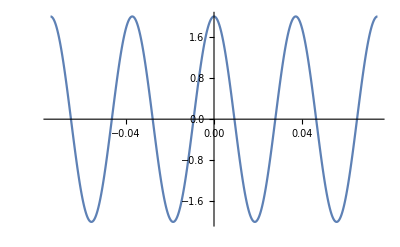

```mathematica
ListLinePlot[DadosTotOndaEsta]
```

```mathematica
Round[k a3]
```

```mathematica
44
```

```mathematica
k a1//N
```

0.435014

```mathematica
FzDataA1=ParallelTable[{zo,ForceZEstacionaria[zo,f,a1,Round[k a1]+5]},{zo,-4π/k,4π/k,π/(50k)}];
(*FzDataA2=ParallelTable[{zo,ForceZEstacionaria[zo,f,a2,10]},{zo,-4π/k,4π/k,π/(50k)}];*)
```

```mathematica
FzDataA3=ParallelTable[{zo,4 ForceZEstacionaria[zo,f,a3,Round[k a3]+5]},{zo,-4π/k,4π/k,π/(50k)}];
```

```mathematica
FMax=Max[Join[Abs[FzDataA1[[All,2]]],Abs[FzDataA3[[All,2]]]]];
```

```mathematica
DadosTotOndaEsta2D=Table[ParallelMap[{#[[1]],y,#[[2]]}&,DadosTotOndaEsta],{y,-17FMax/10,17FMax/10,FMax/10}];
```

```mathematica
ImgFundo=ListDensityPlot[Flatten[DadosTotOndaEsta2D,1],ColorFunction->(Opacity[0.3#,Blue]&),AspectRatio->1/2]
```

-Graphics-

```mathematica
ImgStandingWave=Show[ListLinePlot[{FzDataA1,FzDataA3},FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotRange->{{-0.04,0.04},{-4,4}},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Blue}},PlotRange->All,AspectRatio->1/2,InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,FrameLabel->{"z (m)","F_z (arb. uni.)"}],ImgFundo,Graphics[Text[Style["F_z ka="<>ToString[Round[k a1,0.1]],FontFamily->"Helvetica",Red,Bold,18],{0.031,3.5},{0,0}]],Graphics[Text[Style["F_z×4 ka="<>ToString[Round[k a3,1]],FontFamily->"Helvetica",Blue,Bold,18],{0.031,3},{0,0}]],Epilog->{Inset[Insercoes,{0,0},Automatic,Scaled[.05]],Inset[Insercoes,{-0.0373,0},Automatic,Scaled[.05]],Inset[Insercoes,{0.0373,0},Automatic,Scaled[.05]]},ImageSize->800]
```

-Graphics-

```mathematica
Insercoes1=Graphics[{EdgeForm[Directive[Thick,Black]],Red,Disk[{0.001,0.001}]}];
```

```mathematica
Export["stationarywaveforce.png",ImgStandingWave,ImageSize->800,ImageResolution->500]
```

stationarywaveforce.png

```mathematica
Export["StandingWaveForce.tiff",ImgStandingWave,ImageSize->800,ImageResolution->500,"ImageEncoding"->"LZW"]
```

StandingWaveForce.tiff

```mathematica
Insercoes1=Graphics[{EdgeForm[Directive[Thick,Black]],Red,Disk[{0.001,0.001}]}];
```

```mathematica
ImgStandingWave1=Show[ListLinePlot[{FzDataA1},FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotRange->{{-0.04,0.04},{-4,4}},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Blue}},PlotRange->All,AspectRatio->1/2,InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,FrameLabel->{"z (m)","F_z (arb. uni.)"}],ImgFundo,Graphics[Text[Style["F_z ka="<>ToString[Round[k a1,0.1]],FontFamily->"Helvetica",Red,Bold,16],{0.031,3.5},{0,0}]],Epilog->{Inset[Insercoes1,{0,0},Automatic,Scaled[.05]],Inset[Insercoes1,{-0.0373,0},Automatic,Scaled[.05]],Inset[Insercoes1,{0.0373,0},Automatic,Scaled[.05]],Inset[Insercoes1,{0.0187,0},Automatic,Scaled[.05]],Inset[Insercoes1,{-0.0187,0},Automatic,Scaled[.05]]},ImageSize->800]
```

-Graphics-

```mathematica
ImgStandingWave2=Show[ListLinePlot[{FzDataA3},FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotRange->{{-0.04,0.04},{-4,4}},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotStyle->{{Thickness[0.005],Blue}},PlotRange->All,AspectRatio->1/2,InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,FrameLabel->{"z (m)","F_z (arb. uni.)"}],ImgFundo,Graphics[Text[Style["F_z×4 ka="<>ToString[Round[k a3,1]],FontFamily->"Helvetica",Blue,Bold,16],{0.031,3.5},{0,0}]],Epilog->{Inset[Insercoes2,{-0.0277,0},Automatic,Scaled[.05]],Inset[Insercoes2,{+0.0277,0},Automatic,Scaled[.05]],Inset[Insercoes2,{0.0091,0},Automatic,Scaled[.05]],Inset[Insercoes2,{-0.0091,0},Automatic,Scaled[.05]]},ImageSize->800]
```

-Graphics-

```mathematica
Insercoes2=Graphics[{EdgeForm[Directive[Thick,Black]],Blue,Disk[{0.001,0.001}]}];
```

```mathematica
GraphicsGrid[{{ImgStandingWave1},{ImgStandingWave2}},ImageSize->600,Frame->None,Spacings->{-30, -10}]
```

-Graphics-

```mathematica
Gerar a força em funcao do tamanho
```

```mathematica
FzDataR=ParallelTable[{k R,ForceZEstacionaria[0,f,R,Round[k R+5]]},{R,1/10,100,1}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating SphericalBesselJ[0,4000 π].

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{1/10,-8.26784},{11/10,-67.1194},{21/10,-22.1038},{31/10,-5.17093},{41/10,-22.8332},{51/10,7.20045},{61/10,-2.43975},{71/10,-16.91},{81/10,-52.1402},{91/10,-0.673477},{101/10,-18.8376},{111/10,-16.8307},{121/10,1.29551},{131/10,-111.397},{141/10,-11.8961},{151/10,4.89393},{161/10,11.2441},{171/10,-10.4633},{181/10,20.5854},{191/10,4.57294},{201/10,-11.1717},{211/10,-31.6105},{221/10,3.55607},{231/10,-17.0837},{241/10,-12.4889},{251/10,4.37601},{261/10,254.189},{271/10,-9.36529},{281/10,7.9758},{291/10,10.5521},{301/10,-8.85777},{311/10,35.1131},{321/10,5.49282},{331/10,-10.4518},{341/10,-22.1223},{351/10,4.62859},{361/10,-19.4792},{371/10,-10.6011},{381/10,5.61536},{391/10,49.9379},{401/10,-8.37161},{411/10,10.2484},{421/10,9.44321},{431/10,-8.34519},{441/10,85.1553},{451/10,5.70426},{461/10,-10.6904},{471/10,-17.0488},{481/10,5.16052},{491/10,-25.1482},{501/10,-9.43406},{511/10,6.51727},{521/10,27.5318},{531/10,-7.84248},{541/10,12.8951},{551/10,8.51954},{561/10,-8.22768},{571/10,-251.55},{581/10,5.74882},{591/10,-11.4828},{601/10,-13.9568},{611/10,5.54296},{621/10,-38.4339},{631/10,-8.63089},{641/10,7.39689},{651/10,19.0564},{661/10,-7.54453},{671/10,16.7072},{681/10,7.80267},{691/10,-8.34538},{701/10,-51.6677},{711/10,5.7605},{721/10,-12.8457},{731/10,-11.9064},{741/10,5.89707},{751/10,-90.6586},{761/10,-8.05555},{771/10,8.40123},{781/10,14.6692},{791/10,-7.39731},{801/10,23.23},{811/10,7.25549},{821/10,-8.65764},{831/10,-29.1827},{841/10,5.78552},{851/10,-15.0149},{861/10,-10.4693},{871/10,6.27912},{881/10,216.029},{891/10,-7.64078},{901/10,9.66037},{911/10,12.0249},{921/10,-7.36798},{931/10,37.5228},{941/10,6.84271},{951/10,-9.17174},{961/10,-20.5333},{971/10,5.84397},{981/10,-18.5771},{991/10,-9.4248}}

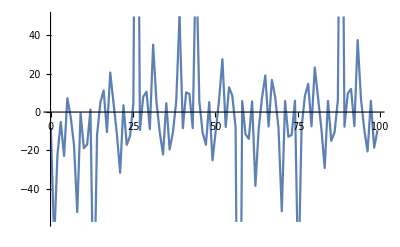

```mathematica
ListLinePlot[FzDataR]
```

```mathematica
FxyData=ParallelTable[{zo,ForceXYEstacionaria[zo,40000,a1,2]},{zo,-50000ka,50000ka,1000 ka}];
FxData=Transpose[{FxyData[[All,1]],FxyData[[All,2]][[All,1]]}];
FyData=Transpose[{FxyData[[All,1]],FxyData[[All,2]][[All,2]]}];
```

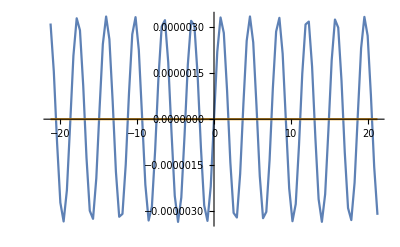

```mathematica
ListLinePlot[{FxData,FyData}]
```

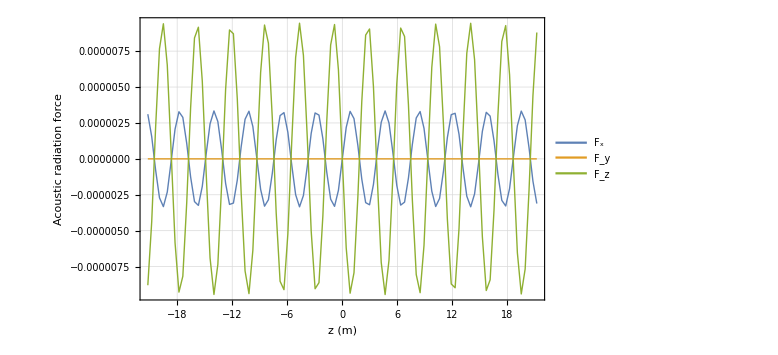

```mathematica
ListLinePlot[{-FxData,-FyData,FzData},PlotTheme->"Detailed",PlotLegends->Placed[{HoldForm["F_x"],HoldForm["F_y"],HoldForm["F_z"]},{Right,Top}],LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm["z (m)"],24,Black],Style[HoldForm["Acoustic radiation force"],24,Black]},PlotRange->All,FrameTicksStyle->Directive[Black,18],ImageSize->Large,PlotStyle->{{Thick}}]
```

## Onda Bessel

Alem do mais, incluir as 4 figuras, mostrando a reconstrução e a exato.

```mathematica
GbesDes[l_,m_] =4π BesselJ[m,ρ0 2π f /cE  Sin[β]]ⅈ^(l-m) Conjugate[SphericalHarmonicY[l,m,β,ϕ0]]Exp[-ⅈ 2π f /cE z0 Cos[β]]KroneckerDelta[o,m];
```

```mathematica
Gbes[l_,m_,β_,z0_,o_]=ⅈ^(l-m)Sqrt[(2l+1) 4π]Sqrt[((l-m)!)/((l+m)!)]LegendreP[l,m,Cos[β]]Exp[-ⅈ 2π f/cE Cos[β] z0]KroneckerDelta[o,m];
```

```mathematica
Clm2[l_,m_,f_,a_,β_,z0_,o_]:= Gbes[l,m,β,z0,o]( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Alm2[l_,m_,f_,a_,β_,z0_,o_]:= Gbes[l,m,β,z0,o]( ( DH[l,2π f /cE a]SphericalBesselJ[l,2π f /cE a]-SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cE a])/(SphericalBesselJ[l,2π f /cI a] DH[l,2π f /cE a]- SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cI a]/α))  ;
PespBes[r_,θ_,ϕ_,f_,a_,β_,z0_,o_]:=Sum[SphericalHankelH1[l,2π f /cE r] SphericalHarmonicY[l,m,θ,ϕ] Clm2[l,m,f,a,β,z0,o],{l,0,NMax},{m,-l,l}]
PincBes[r_,θ_,ϕ_,f_,β_,z0_,o_]:=Sum[SphericalBesselJ[l,2π f /cE r]SphericalHarmonicY[l,m,θ,ϕ] Gbes[l,m,β,z0,o],{l,0,NMax},{m,-l,l}]
PintBes[r_,θ_,ϕ_,f_,a_,β_,z0_,o_]:=Sum[SphericalBesselJ[l,2π f /cI r]SphericalHarmonicY[l,m,θ,ϕ] Alm2[l,m,f,a,β,z0,o],{l,0,NMax},{m,-l,l}]
PTotBes[r_,θ_,ϕ_,f_,a_,β_,z0_,o_]:=Piecewise[{{PintBes[r,θ,ϕ,f,a,β,z0,o],r<a},{PespBes[r,θ,ϕ,f,a,β,z0,o]+PincBes[r,θ,ϕ,f,β,z0,o],r≥a}}]
```

```mathematica
PincBesDes[r_,θ_,ϕ_,f_,a_,β_,z0_,o_]:=
```

```mathematica
pontos=20;
a1=1/10000;
samplePoints=3720;
f=10000000;
k=2π f /cE ;
ka=k a1;
GridXY1=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-3 ka/2,3 ka/2,ka/pontos},{y,-3 ka/2,3 ka/2,ka/pontos}],1],{0,0}],samplePoints];
```

```mathematica
ka//N
```

4.23967

## Reconstrução Bessel

```mathematica
DadosTot1Bessel=ParallelMap[{#[[1]],#[[2]],N[Abs[PincBes[Sqrt[#[[1]]^2+#[[2]]^2]/(2π 40000 /cE),π/2,ArcTan[#[[1]],#[[2]]],40000,β,0,0]]]}&,GridXY1];
DadosTot1BesselOrdem1=ParallelMap[{#[[1]],#[[2]],N[Abs[PincBes[Sqrt[#[[1]]^2+#[[2]]^2]/(2π 40000 /cE),π/2,ArcTan[#[[1]],#[[2]]],40000,β,0,2]]]}&,GridXY1];

figura1=ListDensityPlot[DadosTot1Bessel,PlotRange->All,ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,m=0",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{"x (ka)","y (ka)"}]

figura2=ListDensityPlot[DadosTot1BesselOrdem1,PlotRange->All,ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,m=2",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{"x (ka)","y (ka)"}]
```

Aqui temos que reconstruir as forças Fx,Fy, para as duas ordens investigadas.

```mathematica
Reconstrução Bessel Deslocado
```

```mathematica
β=π/4;
```

```mathematica
GridXY1Deslocado=DeleteCases[Flatten[ParallelTable[{x,y},{x,0,2XMax,2XMax/20},{y,0,2XMax,2XMax/20}],1],{0,0}];
```

```mathematica
GbesDes[l_,m_,f_,z0_,ρ0_,ϕ0_,β_,o_]:=4π BesselJ[m,ρ0 2π f/cE  Sin[β]]ⅈ^(l-m) Conjugate[SphericalHarmonicY[l,m,β,ϕ0]]Exp[-ⅈ 2π f /cE z0 Cos[β]]KroneckerDelta[0,m];
```

```mathematica
PincBesDes[r_,θ_,ϕ_,f_,z0_,ρ0_,ϕ0_,o_]:=Sum[SphericalBesselJ[l,2π f /cE r]SphericalHarmonicY[l,m,θ,ϕ] GbesDes[l,m,f,z0,ρ0,ϕ0,β,o],{l,0,NMax},{m,-l,l}];
```

```mathematica
x0=10;
y0=10;
```

```mathematica
DadosTot1BesselDeslocado=ParallelMap[{#[[1]],#[[2]],N[Abs[PincBesDes[Sqrt[#[[1]]^2+#[[2]]^2]/(2π 40000 /cE),π/2,ArcTan[#[[1]],#[[2]]],40000,0,Sqrt[x0^2+y0^2]/(2π 40000 /cE),ArcTan[x0,y0],0]]]}&,GridXY1Deslocado];
```

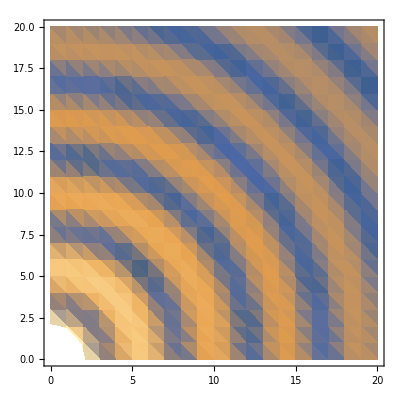

```mathematica
ListDensityPlot[DadosTot1BesselDeslocado]
```

### Exato Bessel

```mathematica
θ=π/2;ordem=0;f=40000;
XMax=10;
figura3=DensityPlot[N[Abs[Exp[ⅈ 2π f /cE Sqrt[x^2+y^2] Cos[θ]Cos[β]]BesselJ[ordem,2π f /cE Sqrt[x^2+y^2]/(2π 40000 /cE) Sin[β]Sin[θ]]Exp[ⅈ ordem ArcTan[x,y]]]],{x,-XMax,XMax},{y,-XMax,XMax},PlotRange->All,ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,m=0",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{"x (ka)","y (ka)"},PlotPoints->150]
Clear[θ,f,ordem];
```

-Graphics-

```mathematica
θ=π/2;ordem=0;
Clear[ka]
figura5=DensityPlot[N[Abs[Exp[ⅈ z Cos[β]]BesselJ[ordem,x Sin[β]]]],{z,-15 ka/2,15 ka/2},{x,-5 ka/2,5 ka/2},PlotRange->All,ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,m=0",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotPoints->150]
Clear[θ,f,ordem];
```

```mathematica
θ=π/2;ordem=2;
figura4=DensityPlot[N[Abs[Exp[ⅈ 2π f /cE Sqrt[x^2+y^2] Cos[θ]Cos[β]]BesselJ[ordem,2π f /cE Sqrt[x^2+y^2]/(2π f /cE) Sin[β]Sin[θ]]Exp[ⅈ ordem ArcTan[x,y]]]],{x,-XMax,XMax},{y,-XMax,XMax},PlotRange->All,ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,m=0",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{"x (ka)","y (ka)"},Exclusions->None,PlotPoints->150]
Clear[θ,f,ordem];
```

```mathematica
figuraTotal=Legended[GraphicsGrid[{{figura3,figura1},{figura4,figura2}},ImageSize->Full],Placed[BarLegend[{"DarkRainbow",{-1,1}},LegendMarkerSize->1000,LegendLayout->"Row",Ticks->None],Below]]
```

```mathematica
Força para feixe de Bessel em xy
```

```mathematica
ForceXYBessel[ρ0_,ϕ0_,z0_,β_,o_,f_,a_,Nmax_Integer?Positive]:=Module[{Cp},
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_]= ( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));
Cp=Table[(2Clm[l] Conjugate[Clm[l+1]]+Clm[l]+Conjugate[Clm[l+1]]),{l,0,Nmax+2}];
Gbes[l_,m_] =4π BesselJ[m,ρ0 2π f /cE  Sin[β]]ⅈ^(l-m) Conjugate[SphericalHarmonicY[l,m,β,ϕ0]]Exp[-ⅈ 2π f /cE z0 Cos[β]]KroneckerDelta[o,m]  ;
-N[ReIm[Sum[ⅈ/(4Sqrt[(2l+1)(2l+3)])(Sqrt[(l-m+1)(l-m)]Cp[[l+1]]Gbes[l,m]Conjugate[Gbes[l+1,m]]+Sqrt[(l+m+2)(l+m+1)]Conjugate[Cp[[l+1]]]Gbes[l+1,m+1]Conjugate[Gbes[l,m]]),{l,0,Nmax},{m,-l,l}] ]]]
```

```mathematica
ForceXYBessel[Sqrt[9+9],ArcTan[-3,-3],0,π/4,2,f,a1,Round[ka+5]]//N
```

ForceXYBessel[4.24264,-2.35619,0.,0.785398,2.,40000.,0.00059,Round[5.+ka]]

```mathematica
temp=ParallelTable[{y,ForceXYBessel[y/k,0,0,π/4,0,f,a1,Round[ka+5]][[1]]},{y,1/100,XMax,XMax/20}];
```

```mathematica
Forca2D=ParallelTable[{{xx,y},ForceXYBessel[Sqrt[xx^2+y ^2]/k,ArcTan[xx,y],0,π/4,0,f,a1,Round[ka+5]]},{xx,1/100,XMax,XMax/20},{y,1/100,XMax,XMax/20}];
```

$Aborted

```mathematica
GridXY1=DeleteCases[Flatten[ParallelTable[{x,y},{x,-XMax,XMax,XMax/15},{y,-XMax,XMax,XMax/15}],1],{0,0}];
```

```mathematica
Forca2D=ParallelMap[{{#[[1]],#[[2]]},ForceXYBessel[Sqrt[#[[1]]^2+#[[2]] ^2]/k,ArcTan[#[[1]],#[[2]]],0,π/4,0,f,a1,Round[ka+5]]}&,GridXY1];
```

```mathematica
figura4
```

```mathematica
Show[figura3,ListVectorPlot[Forca2D,VectorStyle->White,VectorPoints->All]]
```

-Graphics-

```mathematica
StreamPlot
```

```mathematica
Gbes[l_,m_,β_,z0_,o_]=ⅈ^(l-m)Sqrt[(2l+1) 4π]Sqrt[((l-m)!)/((l+m)!)]LegendreP[l,m,Cos[β]]Exp[-ⅈ 2π f/cE Cos[β] z0]KroneckerDelta[o,m];
f=40000000;
β=π/4;
a=1/20;
```

```mathematica
CoeficienteC[l_,f_,a_]:=(α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/
(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]);
```

```mathematica
NMax=25;
```

```mathematica
forcazbessel[f_,a_,β_,z0_,o_]:= Im[Sum[Sqrt[(l-m+1 )( l+m+1)/((2l+1)(2l+3))](2CoeficienteC[l,f,a] Conjugate[CoeficienteC[l+1,f,a]]+CoeficienteC[l,f,a]+Conjugate[CoeficienteC[l+1,f,a]])Gbes[l,m,β,z0,o] Conjugate[Gbes[l+1,m,β,z0,o]],{l,0,NMax},{m,-l,l}] ];
```

```mathematica
graficozforcazbessel=Sort[ParallelTable[{z0,forcazbessel[40000,a,π/4,z0,0]},{z0,-10a,10a,a}]];
```

```mathematica
ListLinePlot[graficozforcazbessel]
```

```mathematica
Força Bessel eixo x-y
kE=Rationalize[2π 40000000/cE a2]
a2
```

```mathematica
CoeficienteBesselXY[l_,m_,ρ0_,kE_,β_,ϕ0_,z0_]= Sum[4π BesselJ[m,ρ0 kE Sin[β]]ⅈ^(l-m) Conjugate[SphericalHarmonicY[l,m,β,ϕ0]]Exp[ⅈ kE z0 Cos[β]],{l,0,NMax},{m,-l,l}];
NovoC[l_,f_,a_]:=(2CoeficienteC[l,f,a]Conjugate[CoeficienteC[l+1,f,a]]+CoeficienteC[l,f,a]+Conjugate[CoeficienteC[l+1,f,a]])
forcaxbessel[f_,a_,ρ0_,kE_,β_,ϕ0_,z0_]:=
Re[Sum[ⅈ/Sqrt[(2l+1) (2l+3)](Sqrt[(l-m+1) (l-m)] NovoC[l,f,a] CoeficienteBesselXY[l,m+1,ρ0,kE,β,ϕ0,z0] Conjugate[CoeficienteBesselXY[l+1,m,ρ0,kE,β,ϕ0,z0]]+Sqrt[(l+m+2) (l+m+1)] Conjugate[NovoC[l,f,a]]CoeficienteBesselXY[l+1,m+1,ρ0,kE,β,ϕ0,z0] Conjugate[CoeficienteBesselXY[l,m,ρ0,kE,β,ϕ0,z0]]),{l,0,NMax},{m,-l,l}]]
```

```mathematica
graficoforcaxbessel=Sort[ParallelTable[forcaxbessel[40000000,a2,ρ0,kE,π/4,0,0],{ρ0,-3a2,3a2}]];
```

```mathematica
ListLinePlot[graficoforcaxbessel,PlotRange->All]
```

```mathematica
forcaybessel[f_,a_,z0_,β_]:=Im[Sum[ⅈ/Sqrt[(2l+1) (2l+3)](NovoC[l,f,a] Gbes[l,m,z0,β] Conjugate[Gbes[l+1,m,f,z0,β]]Sqrt[(l-1) (l+1)]+Conjugate[NovoC[l,f,a]]Gbes[l+1,m,z0,β] Conjugate[Gbes[l,m,z0,β]]),{l,0,NMax},{m,-l,l}]];
```

```mathematica
graficoforcaybessel=Sort[ParallelTable[{-z0,forcaybessel[40000000,a,z0,0]},{z0,-a,a,a/30}]];
```

```mathematica
ListLinePlot[graficoforcaybessel]
```

```mathematica
forcaemraio=ListLinePlot[{-graficoforcaxbessel,-graficoforcaybessel,graficozforcazbessel},PlotTheme->"Detailed",PlotLegends->Placed[{HoldForm["F_x"],HoldForm["F_y"],HoldForm["F_z"]},{Right,Top}],LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm["z (m)"],24,Black],Style[HoldForm["Acoustic radiation force"],24,Black]},PlotRange->All,FrameTicksStyle->Directive[Black,18],ImageSize->Large,PlotStyle->{{Thick}}]
```

## Outros

```mathematica
Qualqeur outro programa vem aqui.
```

## Carregar/salvar

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/matheus/Desktop

```mathematica
DumpSave["SimulacoesNOVA.mx","Global`"]
```

{Global`}

```mathematica
<<"Simulacoes.mx"
```

```mathematica
ListDensityPlot[DadosTot1Bessel2,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,PlotLegends->Placed[Automatic,Below],PlotLabel->"β=π/4",LabelStyle->{Black,20},FrameStyle->{Black,20},ColorFunction->"TemperatureMap",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameTicks->None]
```

```mathematica
Export["BesselBeam.png",ListDensityPlot[DadosTot1Bessel,PlotRange->{{-0.05,0.1},{-0.06,0.06}},AspectRatio->Automatic,ImageSize->Large,PlotLegends->Placed[Automatic,Below],PlotLabel->"β=π/4",LabelStyle->{Black,20},FrameStyle->{Black,20},ColorFunction->"TemperatureMap",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameTicks->None],ImageResolution->500]
```

```mathematica
Export["EspBesselBeam.png",Show[ListDensityPlot[EspBessel,PlotRange->{{-2.7 a1/2,4a1/2},{-3 a1/2,3 a1/2},All},AspectRatio->Automatic,ImageSize->Large,PlotLegends->Placed[Automatic,Below],PlotLabel->"ka=30",LabelStyle->{Black,20},FrameStyle->{Black,20},ColorFunction->"TemperatureMap",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",FrameTicks->None,PlotRangePadding->None,Frame->True,ColorFunctionScaling->True],Graphics[{Black,Dashed, Thick,Circle[{0,0},a1]}]],ImageResolution->500]
```

```mathematica
EspBessel=ParallelMap[{#[[1]],#[[2]],N[Abs[PTotBes[Sqrt[#[[1]]^2+#[[2]]^2],ArcTan[#[[1]],#[[2]]],0,136803,a1,π/4,z]],50]}&,GridXY1];
```

```mathematica
Show[ListDensityPlot[EspBessel,PlotRange->{{-2.7 a1/2,4a1/2},{-3 a1/2,3 a1/2},All},AspectRatio->Automatic,ImageSize->Large,PlotLegends->Placed[Automatic,Below],PlotLabel->"ka=30",LabelStyle->{Black,20},FrameStyle->{Black,20},ColorFunction->"TemperatureMap",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",FrameTicks->None,PlotRangePadding->None,Frame->True,ColorFunctionScaling->True],Graphics[{Black,Dashed, Thick,Circle[{0,0},a1]}]]
```

```mathematica
PincBes[2  10^(-6),1,0,40000,β,0]//N
```

```mathematica
Plot[Abs[PincBes[z,0,0,40000,β,0/10]],{z,-0.5,0.5},PlotRange->All]
```

```mathematica
DensityPlot[Abs[PincBes[Sqrt[x^2+y^2],π/2,ArcTan[x,y],40000,β,0]],{x,-0.1,0.1},{y,-0.1,0.1},PlotRange->All]
```

```mathematica
DensityPlot[Abs[PincBes[Sqrt[x^2+y^2],ArcTan[x,y],0,40000,β,0]],{x,-3 10^(-6),10 10^(-6)},{y,-4 10^(-6),4 10^(-6)}]
```

```mathematica
Gnpw=Re[ParallelTable[Sum[ 2 *LegendreP[l,m,Cos[β]]Sqrt[(2l+1)/(4π)]SphericalBesselJ[l,2π f /cI a1]SphericalHarmonicY[l,m,0,0],{l,0,55},{m,-l,l}],{β,0,40}]];
```

```mathematica
ListPlot[Gnpw,Joined->True]
```